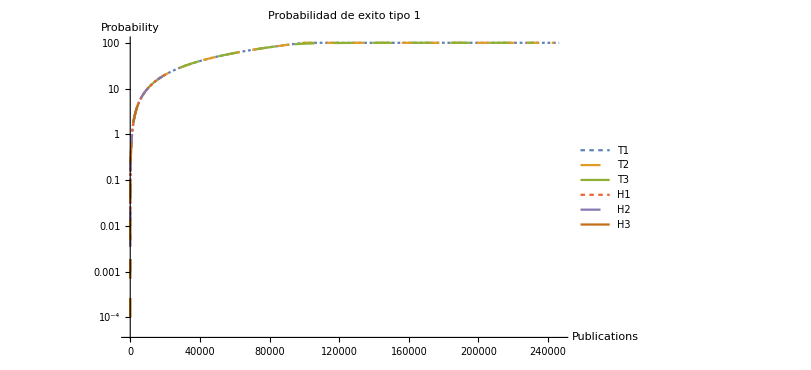
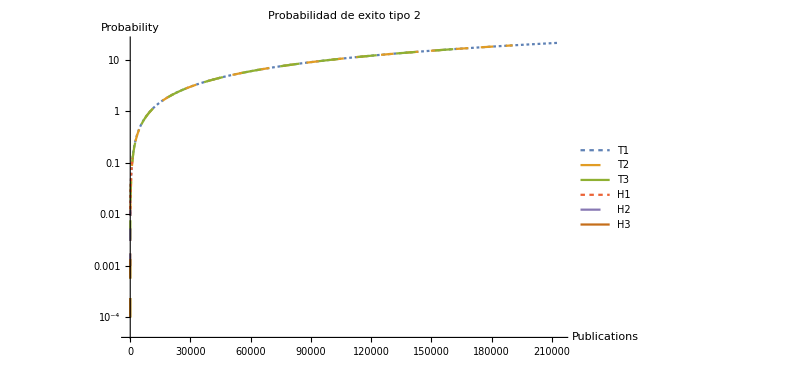
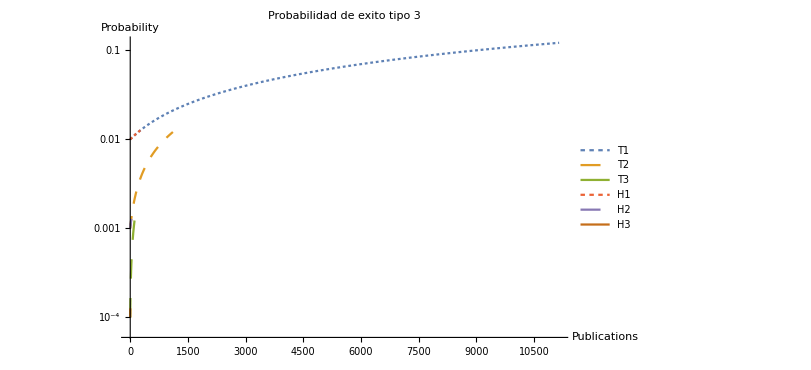
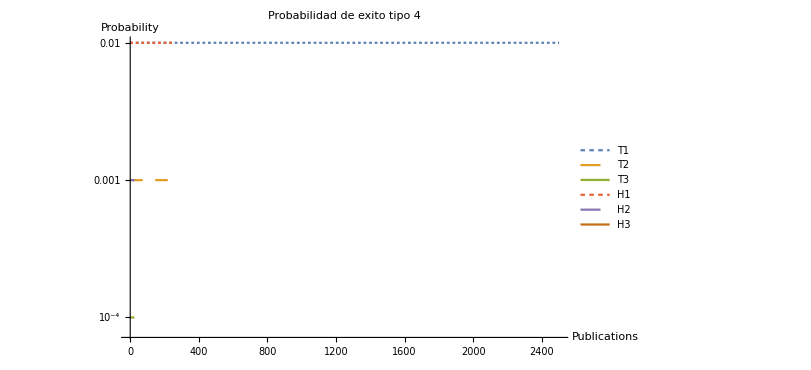
-Graphics- | -Graphics-
-Graphics- | -Graphics-

```mathematica
y = "/home/fabianact/ActualTesis/Tesis/ModelosPresentados/SinCompetencia";
SetDirectory[y<>"/images"];
pub1= Import[y<>"/averageResults/pub-prob-1-0.01-curve.csv"];
pub2= Import[y<>"/averageResults/pub-prob-1-0.001-curve.csv"];
pub3= Import[y<>"/averageResults/pub-prob-1-1.0E-4-curve.csv"];
pub4 = Import[y<>"/averageResults/pub-prob-5-0.01-curve.csv"];
pub5 = Import[y<>"/averageResults/pub-prob-5-0.001-curve.csv"];
pub6 = Import[y<>"/averageResults/pub-prob-5-1.0E-4-curve.csv"];
plotPub1= Show[ListLogPlot[{ pub1, pub2, pub3, pub4, pub5, pub6 },ImageSize->600,  AxesLabel->{"Publications","Probability"},Joined->True, PlotLegends->{ "T1",  "T2", "T3",  "H1",  "H2",  "H3"},PlotRange->All,PlotLabel-> "Probabilidad de exito tipo 1",PlotStyle->{Dashing[Tiny],Dashing[Medium], Dashing[Large], Dashing[Tiny], Dashing[Medium], Dashing[Large]}]];

Export["pub-prob-1.png",plotPub];

pub1= Import[y<>"/averageResults/pub-prob-2-0.01-curve.csv"];
pub2= Import[y<>"/averageResults/pub-prob-2-0.001-curve.csv"];
pub3= Import[y<>"/averageResults/pub-prob-2-1.0E-4-curve.csv"];
pub4 = Import[y<>"/averageResults/pub-prob-6-0.01-curve.csv"];
pub5 = Import[y<>"/averageResults/pub-prob-6-0.001-curve.csv"];
pub6 = Import[y<>"/averageResults/pub-prob-6-1.0E-4-curve.csv"];
plotPub2 = Show[ListLogPlot[{ pub1, pub2, pub3, pub4, pub5, pub6 },ImageSize->600,  AxesLabel->{"Publications","Probability"},Joined->True, PlotLegends->{ "T1",  "T2", "T3",  "H1",  "H2",  "H3"},PlotRange->All,PlotLabel-> "Probabilidad de exito tipo 2", PlotStyle->{Dashing[Tiny],Dashing[Medium], Dashing[Large], Dashing[Tiny], Dashing[Medium], Dashing[Large]}]];
Export["pub-prob-2.png",plotPub];

pub1= Import[y<>"/averageResults/pub-prob-3-0.01-curve.csv"];
pub2= Import[y<>"/averageResults/pub-prob-3-0.001-curve.csv"];
pub3= Import[y<>"/averageResults/pub-prob-3-1.0E-4-curve.csv"];
pub4 = Import[y<>"/averageResults/pub-prob-7-0.01-curve.csv"];
pub5 = Import[y<>"/averageResults/pub-prob-7-0.001-curve.csv"];
pub6 = Import[y<>"/averageResults/pub-prob-7-1.0E-4-curve.csv"];
plotPub3 = Show[ListLogPlot[{ pub1, pub2, pub3, pub4, pub5, pub6 },ImageSize->600,  AxesLabel->{"Publications","Probability"},Joined->True, PlotLegends->{ "T1",  "T2", "T3",  "H1",  "H2",  "H3"},PlotRange->All,PlotRange->All,PlotLabel-> "Probabilidad de exito tipo 3",PlotStyle->{Dashing[Tiny],Dashing[Medium], Dashing[Large], Dashing[Tiny], Dashing[Medium], Dashing[Large]}]];
Export["pub-prob-3.png",plotPub];

pub1= Import[y<>"/averageResults/pub-prob-4-0.01-curve.csv"];
pub2= Import[y<>"/averageResults/pub-prob-4-0.001-curve.csv"];
pub3= Import[y<>"/averageResults/pub-prob-4-1.0E-4-curve.csv"];
pub4 = Import[y<>"/averageResults/pub-prob-8-0.01-curve.csv"];
pub5 = Import[y<>"/averageResults/pub-prob-8-0.001-curve.csv"];
pub6 = Import[y<>"/averageResults/pub-prob-8-1.0E-4-curve.csv"];
plotPub4 = Show[ListLogPlot[{ pub1, pub2, pub3, pub4, pub5, pub6 },ImageSize->600,  AxesLabel->{"Publications","Probability"},Joined->True, PlotLegends->{ "T1",  "T2", "T3",  "H1",  "H2",  "H3"},PlotRange->All, PlotRange->All,PlotLabel-> "Probabilidad de exito tipo 4",PlotStyle->{Dashing[Tiny],Dashing[Medium], Dashing[Large], Dashing[Tiny], Dashing[Medium], Dashing[Large]}]];
Export["pub-prob-4.png",plotPub];

pubTotal=Grid[{{plotPub1,plotPub2},{plotPub3,plotPub4}}]
Export["pub-prob-total.png",pubTotal];
```